```mathematica
Kp=1
taus=31
zeta=.21

# Transfer Function
# Kp/(taus*s**2+2*zeta*taus*s+1)
num=[Kp]
den=[taus**2,2.0*zeta*taus,1]
```

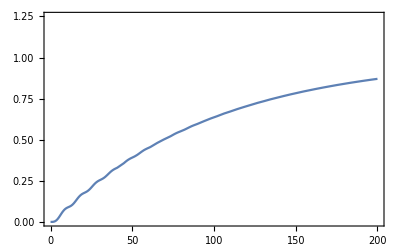

```mathematica
{q,p}={6,.05};
rf[s_]:=1/s* (q (1+s))/(q+5 s (1+3 s+2 s^2))*(p (1+s))/(p+5 s (1+3 s+2 s^2))
Plot[
InverseLaplaceTransform[rf[s],s,t]
,{t,0,200}
,Frame->True
,PlotRange->{{0,200},{0,1.25}}
]
```

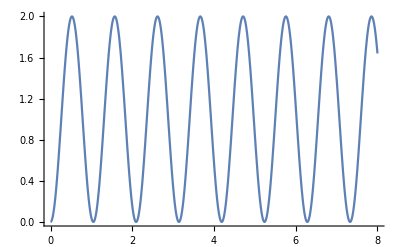
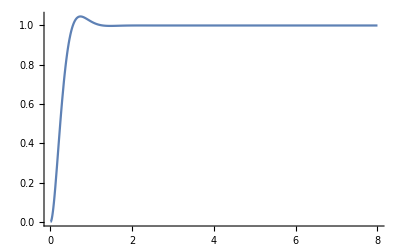
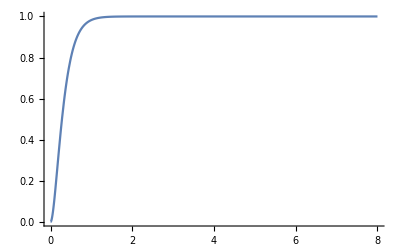
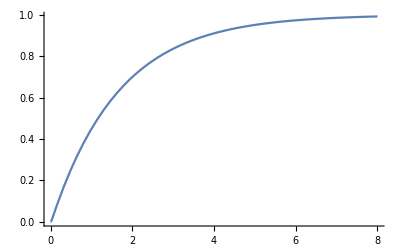
Undamped | 36/(36+s^2)TransferFunctionModelFalseFalseFalseFalse$FailedControl`CommonDump`$DUMMY$Control`CommonDump`$DUMMY$#$CellContext`s1136361FalseFalseFalseAutomaticNoneAutomatic | -Graphics-
Underdamped | 36/(36+8.4 s+s^2)TransferFunctionModelFalseFalseFalseFalse$FailedControl`CommonDump`$DUMMY$Control`CommonDump`$DUMMY$#$CellContext`s1136361FalseFalseFalseAutomaticNoneAutomatic | -Graphics-
Critically damped | 36/(36+12 s+s^2)TransferFunctionModelFalseFalseFalseFalse$FailedControl`CommonDump`$DUMMY$Control`CommonDump`$DUMMY$#$CellContext`s1136361FalseFalseFalseAutomaticNoneAutomatic | -Graphics-
Overdamped | 36/(36+60 s+s^2)TransferFunctionModelFalseFalseFalseFalse$FailedControl`CommonDump`$DUMMY$Control`CommonDump`$DUMMY$#$CellContext`s1136361FalseFalseFalseAutomaticNoneAutomatic | -Graphics-

```mathematica
order2[ζ_,ω_]:=TransferFunctionModel[ω^2/(s^2+2 ζ ω s+ω^2),s];
Table[{
Last[damping],sys=order2[First[damping],6],Plot[OutputResponse[sys,UnitStep[t],t]//Evaluate,{t,0,8},PlotRange->All]
},{damping,{{0,"Undamped"},{0.7,"Underdamped"},{1,"Critically damped"},{5,"Overdamped"}}}]//TableForm
```

```mathematica
sysA[ζA_,ωA_]:=TransferFunctionModel[ωA^2/(s^2+2 ζA* ωA*s+ ωA^2),s];
Plot[OutputResponse[sysA[0,6],UnitStep[t],t]//Evaluate,{t,0,8},PlotRange->All]
```

-Graphics-

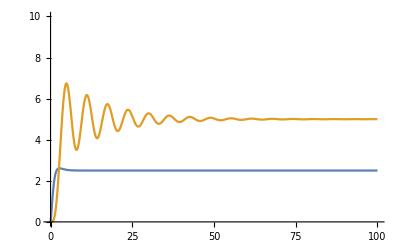

```mathematica
sysA[ζA_,ωA_]:=ωA^2/(s^2+2 ζA* ωA*s+ ωA^2);
range={0,100};
Plot[
{
InverseLaplaceTransform[2.5/s*sysA[1,2]+sysA[1,1],s,t],
InverseLaplaceTransform[5/s*sysA[.075,1]*sysA[1,1],s,t]
}
,{t,range[[1]],range[[2]]}
,PlotRange->{{range[[1]],range[[2]]},{0,10}}
]
```